# Goldratt’s “Dice Game” and the Five Focusing Steps

## A simulation for learning purposes.

© Jürgen Kanz, March 2021

```mathematica
ClearAll["Global`"]
```

## 1. Introduction

The Dice Game was introduced in one of the best-selling business books of all time, THE GOAL, authored by Dr. Eli Goldratt.
The WSU website created by James Holt gives very clear instructions on how to run your own dice game in a group, including all the details for each iteration and what the expected results should be (https://public.wsu.edu/~engrmgmt/holt/em530/Docs/DiceGames.htm).
Meantime several Excel sheets (like https://www.researchgate.net/publication/235301922_An_Excel-based_dice_game_An_integrative_learning_activity_in_operations_management) and special commercial apps (like https://www.goldrattsdicegame.com/) have been developed to simulate the Dice Game.
This notebook is slightly different because we simulate five different scenarios to highlight the interdependencies within the line. The scenario sequence is as follows:

Balanced Line

Constrained Line

TOC - DBR with a focus on the Rope

TLS

Full TOC

For each of the scenarios, we analyze the statistics regarding the roll of dices, the queues between the work stations or work centers (called “stations” in the text), and the financial figures according to the Throughput Accounting.

### 1.1 Rules of the simulation

1. We have unlimited raw material available.
2. We can ship and sell what we produce.
3. Apart from the constrained station, we have two dices that represent the available capacity at each station. The constrained station has only one dice.
4. For comparison reasons, we save the rolled dice points from the Balanced Line scenario and re-use them in all other scenarios apart from the constraint dice result.

### 1.2 Rolling the dices

Please be aware that in case you have one dice and you roll it for example 100,000 times you get an almost Uniform distribution.

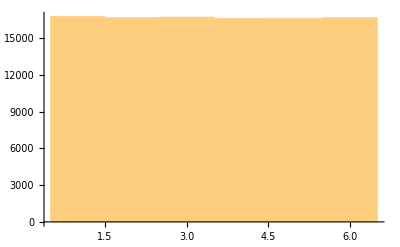

```mathematica
oneDice=Table[RandomInteger[{1,6}],{i,1,100000}];
Histogram[oneDice]
```

Average

```mathematica
averageOneDice=N[Mean[oneDice]]
```

3.49646

Standard Deviation

```mathematica
stdOneDice=N[StandardDeviation[oneDice]]
```

1.70896

If you have two dices and you throw them 100,000 times you get a Normal (Gaussian) distribution.

```mathematica
twoDices=Table[Total[RandomInteger[{1,6},2]],{i,1,100000}];
```

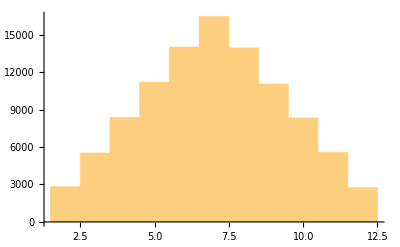

```mathematica
Histogram[twoDices]
```

Average

```mathematica
averageTwoDices=N[Mean[twoDices]]
```

6.9936

Standard Deviation

```mathematica
stdTwoDices=N[StandardDeviation[twoDices]]
```

2.41588

### 1.3 Throughput Accounting

With the Input data and the simulation results, the Throughput Accounting figures can be determined:

Throughput = (Selling Price - Total Variable Cost) * Total Quantity Shipped

Inventory = (Total Ending WIP * Total Variable Cost)  + Investment

Net Profit = Throughput - Operating Expenses

ROI = Net Profit / Inventory

Customer Service = Total Quantity Shipped / Market Demand

Productivity = Throughput / Operating Expenses

Inventory Turnover = Total Quantity Shipped / Ending WIP

### 1.4 The Five Focusing Steps

The Five Focusing Steps belong to the core of TOC - Theory of Constraints. It is a focusing process that helps to manage the constraint(s) in a system.

Identify the Constraint

Exploit the Constraint

Subordinate Everything Else to the Constraint

Elevate the Constraint

Prevent Inertia from Becoming the Constraint

In this simulation we consider all steps during the Dice Game.

## 2. Input of data

INPUT: number of time units in the observed period. This can be seconds, minutes, hours, or days.

```mathematica
timeUnits=100;
```

INPUT: amount of work-in-process in each queue at the beginning of the period

```mathematica
startWipLevel=15;
```

INPUT : Total Variable Cost per produced unit [$]

```mathematica
tvc=200;
```

INPUT : Selling Price per shipped unit [$]

```mathematica
sp= 400;
```

INPUT: Operating Expenses (oe) for the period. OE is typically the summation of Period Expense + Carrying Cost + Improvement Initiative Cost  [$]

```mathematica
oe=30000;
```

INPUT: Needed Investment (invest) in the period in order to fulfill the order(s). [$]

```mathematica
invest=20000;
```

## 3. Calculation for Balanced Line

-Graphics-

The Balanced Line is a typical manufacturing line. Each station has two dices that represent the available capacity of the station. The statistical range per station is ten. Which means that each dice can roll one to six points. The points are added for each station in every round. The number of rounds depends on the variable timeUnits. What station 1 has rolled will be forwarded to station 2 in the form of material. For more details about the process, the reader should study the material as suggested in section 1. Introduction.

### 3.1 Calculation part

```mathematica
SeedRandom[1577];
```

```mathematica
dg=Table[0,{i,timeUnits},{j,19}];
```

```mathematica
Do[
       dg[[i, 1]] = i;
                dg[[i, 2]] = Total[RandomInteger[{1,6}, 2]];
      dg[[i, 3]] =dg[[i, 2]];
                If[i == 1, dg[[i, 4]] = dg[[i, 3]] + startWipLevel,dg[[i, 4]] = dg[[i - 1, 4]] - dg[[i - 1, 6]] + dg[[i, 3]]];
        dg[[i, 5]] = Total[RandomInteger[{1,6}, 2]];
                dg[[i, 6]] =Min[dg[[i, 5]], dg[[i, 4]]];
               If[i == 1, dg[[i, 7]] = dg[[i, 6]] + startWipLevel,dg[[i, 7]] = dg[[i - 1, 7]] - dg[[i - 1, 9]] + dg[[i, 6]]];
    dg[[i, 8]] = Total[RandomInteger[{1,6}, 2]];
                dg[[i, 9]] = Min[dg[[i, 8]], dg[[i, 7]]];
                If[i == 1, dg[[i, 10]] = dg[[i, 9]] + startWipLevel, dg[[i, 10]] = dg[[i - 1, 10]] - dg[[i - 1, 12]] + dg[[i, 9]]];
    dg[[i, 11]] = Total[RandomInteger[{1,6},2]];
                dg[[i, 12]] = Min[dg[[i, 11]], dg[[i, 10]]];
               If[i == 1, dg[[i, 13]] = dg[[i, 12]] + startWipLevel, dg[[i, 13]] = dg[[i - 1, 13]] - dg[[i - 1, 15]] + dg[[i, 12]]];
    dg[[i, 14]] = Total[RandomInteger[{1,6}, 2]];
                dg[[i, 15]] = Min[dg[[i, 14]], dg[[i, 13]]];
                If[i == 1, dg[[i, 16]] = dg[[i, 15]] + startWipLevel , dg[[i, 16]] = dg[[i - 1, 16]] - dg[[i - 1, 18]] + dg[[i, 15]]];
    dg[[i, 17]] = Total[RandomInteger[{1,6}, 2]];
                dg[[i, 18]] = Min[dg[[i, 17]], dg[[i, 16]]];
                dg[[i, 19]] = dg[[i,18]],
 {i,1,timeUnits,1}]
```

```mathematica
totalwipBL1=Total[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]]}];
finishedgoodsBL1=Total[dg[[All,19]]];
BL1=dg;
```

```mathematica
availCap=Table[N[Total[dg[[All,3*i-1]]]],{i,1,6}];
utilCap=Table[N[Total[dg[[All,3*i]]]],{i,1,6}];
```

```mathematica
plot1=BarChart[<|"station 1"-><|"avail."->availCap[[1]],"util."->utilCap[[1]]|>,
"station  2"-><|"avail."->availCap[[2]],"util."->utilCap[[2]]|>,
"station  3"-><|"avail."->availCap[[3]],"util."->utilCap[[3]]|>,
"station  4"-><|"avail."->availCap[[4]],"util."->utilCap[[4]]|>,
"station  5"-><|"avail."->availCap[[5]],"util."->utilCap[[5]]|>,
"station  6"-><|"avail."->availCap[[6]],"util."->utilCap[[6]]|> |>,
ChartStyle->"Pastel",
PlotLabel->"available versus utilized capacity per workstation",
ChartLegends->Placed[{"available capacity","utilized capacity"},Below],
ChartLabels->{{"station 1","station 2","station 3","station 4","station 5","station 6"},None},
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];

plot2=BarChart[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]],Total[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]]}],Style[Total[dg[[All,19]]],Blue]},ChartLabels->{"queue12","queue23","queue34","queue45","queue56","totalwip","finalgoods"},
PlotTheme->"Business",
PlotLabel->"wip per queue, total wip of all queues and final goods",
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];

BL1RollingStat=Dataset[{
<|
"Min"-><|"station 1"->N[Min[dg[[All, 2]]]],"station 2"->N[Min[dg[[All, 5]]]],"station 3"->N[Min[dg[[All, 8]]]],"station 4"->N[Min[dg[[All,11]]]],"station 5"->N[Min[dg[[All,14]]]],"station 6"->N[Min[dg[[All,17]]]]|>,
"Mean"-><|"station 1"->N[Mean[dg[[All, 2]]]],"station 2"->N[Mean[dg[[All, 5]]]],"station 3"->N[Mean[dg[[All, 8]]]],"station 4"->N[Mean[dg[[All,11]]]],"station 5"->N[Mean[dg[[All,14]]]],"station 6"->N[Mean[dg[[All,17]]]]|>,
"Median"-><|"station 1"->N[Median[dg[[All, 2]]]],"station 2"->N[Median[dg[[All, 5]]]],"station 3"->N[Median[dg[[All, 8]]]],"station 4"->N[Median[dg[[All,11]]]],"station 5"->N[Median[dg[[All,14]]]],"station 6"->N[Median[dg[[All,17]]]]|>,
"StandardDeviation"-><|"station 1"->N[StandardDeviation[dg[[All, 2]]]],"station 2"->N[StandardDeviation[dg[[All, 5]]]],"station 3"->N[StandardDeviation[dg[[All, 8]]]],"station 4"->N[StandardDeviation[dg[[All,11]]]],"station 5"->N[StandardDeviation[dg[[All,14]]]],"station 6"->N[StandardDeviation[dg[[All,17]]]]|>,
"Variance"-><|"station 1"->N[Variance[dg[[All, 2]]]],"station 2"->N[Variance[dg[[All, 5]]]],"station 3"->N[Variance[dg[[All, 8]]]],"station 4"->N[Variance[dg[[All,11]]]],"station 5"->N[Variance[dg[[All,14]]]],"station 6"->N[Variance[dg[[All,17]]]]|>,
"Max"-><|"station 1"->N[Max[dg[[All, 2]]]],"station 2"->N[Max[dg[[All, 5]]]],"station 3"->N[Max[dg[[All, 8]]]],"station 4"->N[Max[dg[[All,11]]]],"station 5"->N[Max[dg[[All,14]]]],"station 6"->N[Max[dg[[All,17]]]]|>
|>},HeaderBackground->Pink];

BL1QueueStat=Dataset[{
<|
"Min"-><|"queue 12"->N[Min[dg[[All, 4]]]],"queue 23"->N[Min[dg[[All, 7]]]],"queue 34"->N[Min[dg[[All, 10]]]],"queue 45"->N[Min[dg[[All,13]]]],"queue 56"->N[Min[dg[[All,16]]]],"final goods"->N[Min[dg[[All,18]]]]|>,
"Mean"-><|"queue 12"->N[Mean[dg[[All, 4]]]],"queue 23"->N[Mean[dg[[All, 7]]]],"queue 34"->N[Mean[dg[[All, 10]]]],"queue 45"->N[Mean[dg[[All,13]]]],"queue 56"->N[Mean[dg[[All,16]]]],"final goods"->N[Mean[dg[[All,18]]]]|>,
"Median"-><|"queue 12"->N[Median[dg[[All, 4]]]],"queue 23"->N[Median[dg[[All, 7]]]],"queue 34"->N[Median[dg[[All, 10]]]],"queue 45"->N[Median[dg[[All,13]]]],"queue 56"->N[Median[dg[[All,16]]]],"final goods"->N[Median[dg[[All,18]]]]|>,
"StandardDeviation"-><|"queue 12"->N[StandardDeviation[dg[[All, 4]]]],"queue 23"->N[StandardDeviation[dg[[All, 7]]]],"queue 34"->N[StandardDeviation[dg[[All, 10]]]],"queue 45"->N[StandardDeviation[dg[[All,13]]]],"queue 56"->N[StandardDeviation[dg[[All,16]]]],"final goods"->N[StandardDeviation[dg[[All,18]]]]|>,
"Variance"-><|"queue 12"->N[Variance[dg[[All, 4]]]],"queue 23"->N[Variance[dg[[All, 7]]]],"queue 34"->N[Variance[dg[[All, 10]]]],"queue 45"->N[Variance[dg[[All,13]]]],"queue 56"->N[Variance[dg[[All,16]]]],"final goods"->N[Variance[dg[[All,18]]]]|>,
"Max"-><|"queue 12"->N[Max[dg[[All, 4]]]],"queue 23"->N[Max[dg[[All, 7]]]],"queue 34"->N[Max[dg[[All, 10]]]],"queue 45"->N[Max[dg[[All,13]]]],"queue 56"->N[Max[dg[[All,16]]]],"final goods"->N[Max[dg[[All,18]]]]|>
|>},HeaderBackground->LightBlue];

BL1QueueGraph=TableForm[{{ListLinePlot[dg[[All,4]],PlotLabel->"queue12"],ListLinePlot[dg[[All,7]],PlotLabel->"queue23"],ListLinePlot[dg[[All,10]],PlotLabel->"queue34"]},{ListLinePlot[dg[[All,13]],PlotLabel->"queue45"],ListLinePlot[dg[[All,16]],PlotLabel->"queue56"],ListLinePlot[dg[[All,18]],PlotLabel->"finalgoods"]}},1];

TBL1=(sp-tvc)*finishedgoodsBL1; 
IBL1=(totalwipBL1*tvc)+invest;
npBL1=TBL1-oe;
roiBL1=PercentForm[npBL1/IBL1 /100];
csBL1=PercentForm[1.];
ltBL1=totalwipBL1 / finishedgoodsBL1 / timeUnits;
pBL1=TBL1/oe;
itBL1=finishedgoodsBL1 / totalwipBL1;

financeBL1=Dataset[{
<| "Throughput"-><|"Balanced Line"->N[TBL1]|>,
"Inventory"-><|"Balanced Line"->N[IBL1]|>,
"Operating Expenses"-><|"Balanced Line"->N[oe]|>,
"Net Profit"-><|"Balanced Line"->N[npBL1]|>,
"ROI"-><|"Balanced Line"->N[roiBL1]|>,
"Customer Service"-><|"Balanced Line"->N[csBL1]|>,
"Productivity"-><|"Balanced Line"->N[pBL1]|>,
"Inventory Turnover"-><|"Balanced Line"->N[itBL1]|>
|>},HeaderBackground->LightGreen];
```

### 3.2 Rolling dice statistics

How many points have been rolled in each station? What are the statistical results when we take the results overall timeUnits?

```mathematica
BL1RollingStat
```

The results are in line with the outcome of the two dices in section 1.2 Rolling the dices.

### 3.3 Queue statistics

The Queue statistics are different compared to the Rolling dice statistics. Here we see material among two stations as timelines overall timeUnits.
Isn’t it obvious that our system belongs to the group of dynamic systems? It is recognizable that we have a strong interdependence caused by the variance of each roll of dices among the stations.

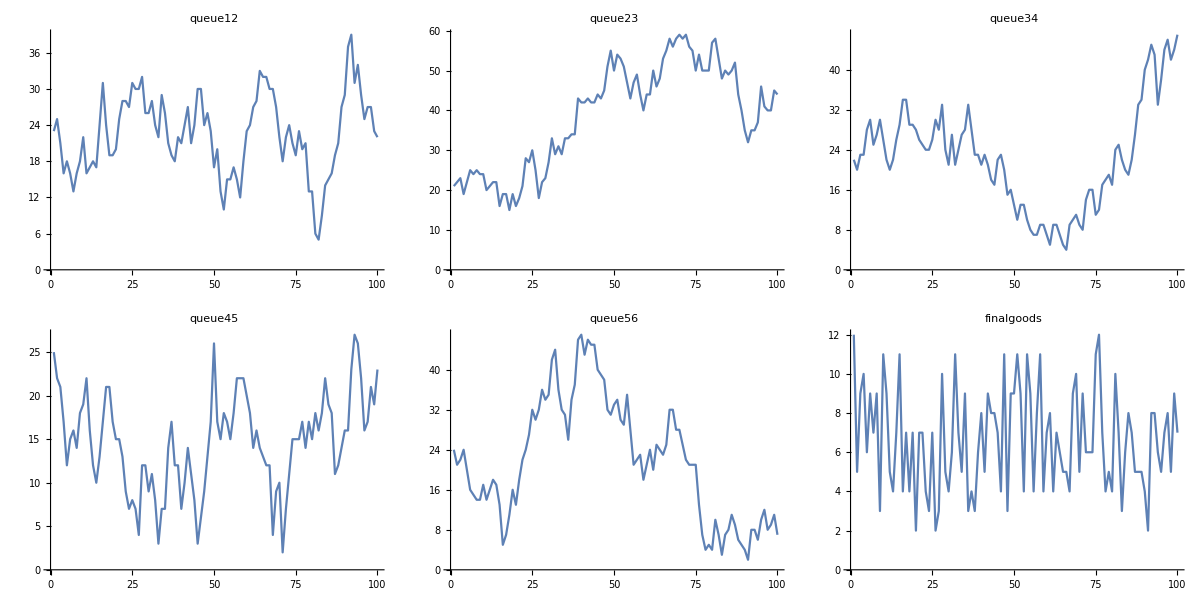

```mathematica
BL1QueueGraph
```

```mathematica
BL1QueueStat
```

Reminder: The table here shows material units/pieces in each queue. Not dice points!

### 3.4 Comparison of a) available and utilized capacities and b) last run WIP plus Final goods

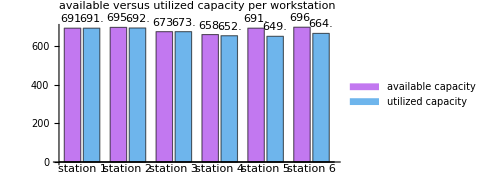
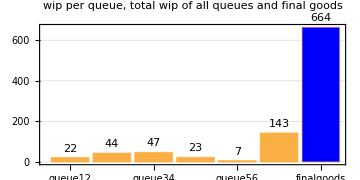
*        **        *-Graphics--Graphics-

```mathematica
Row[{plot1,plot2},"*        *"]
```

A Balanced Line leads to an almost 100% utilization of the available capacity. At the end of our game, we have only 143 pieces in working-in-process (Ending WIP), but we have sold and shipped 664 final goods. An excellent result!
Let us have a look at the financial figures.

### 3.5 Throughput Accounting figures

```mathematica
financeBL1
```

The financial figures of Throughput Accounting confirm the excellent result we have achieved so far. Please be aware that we can sell and ship all final goods independent from the scenario, hence the Customer Service will always be on a level of 100%.
Therefore it is not a wonder that companies strive for balanced lines. But is such a solution realistic?

According to Dr. Eliyahu Goldratt there is always at least one constraint that limits the flow inside a system. Typical reasons are capacities of machines and/or workers are insufficient, Murphy’s Law comes into play “Anything that can go wrong, will go wrong”, or any other thinkable disturbance can limit the flow. In such a case we face a physical bottleneck or in other contexts called a constraint. Our line becomes unbalanced. In the next section, we will analyze a Constrained Line.

## 4. Constrained Line

-Graphics-

For this simulation scenario we reduce the available capacity of station 4. We only use one dice. “Station 4” is now our constraint also for the following scenarios. This also means that we have achieved the first step of the Five Focusing Steps. 
To have a good comparison with the Balanced Line, we re-use the rolled dice points of the remaining stations. The material exchange from station to station has to be re-calculated.

### 4.1 Calculation part

```mathematica
dg=BL1;
Do[
 dg[[i, 1]] = i;
                dg[[i, 2]] = dg[[i, 2]];
                dg[[i, 3]] =dg[[i, 2]];
                If[i == 1, dg[[i, 4]] = dg[[i, 3]] + startWipLevel,dg[[i, 4]] = dg[[i - 1, 4]] - dg[[i - 1, 6]] + dg[[i, 3]]];
    dg[[i, 5]] = dg[[i, 5]];
                dg[[i, 6]] =Min[dg[[i, 5]], dg[[i, 4]]];
               If[i == 1, dg[[i, 7]] = dg[[i, 6]] + startWipLevel,dg[[i, 7]] = dg[[i - 1, 7]] - dg[[i - 1, 9]] + dg[[i, 6]]];
    dg[[i, 8]] = dg[[i, 8]];
                dg[[i, 9]] = Min[dg[[i, 8]], dg[[i, 7]]];
                If[i == 1, dg[[i, 10]] = dg[[i, 9]] + startWipLevel, dg[[i, 10]] = dg[[i - 1, 10]] - dg[[i - 1, 12]] + dg[[i, 9]]]; 
(* constrained by only one dice *) 
 dg[[i, 11]] = Total[RandomInteger[{1,6},1]];
                dg[[i, 12]] = Min[dg[[i, 11]], dg[[i, 10]]];
                If[i == 1, dg[[i, 13]] = dg[[i, 12]] + startWipLevel, dg[[i, 13]] = dg[[i - 1, 13]] - dg[[i - 1, 15]] + dg[[i, 12]]];
 dg[[i, 14]] = dg[[i, 14]];
               dg[[i, 15]] = Min[dg[[i, 14]], dg[[i, 13]]];
               If[i == 1, dg[[i, 16]] = dg[[i, 15]] + startWipLevel , dg[[i, 16]] = dg[[i - 1, 16]] - dg[[i - 1, 18]] + dg[[i, 15]]];
dg[[i, 17]] = dg[[i, 17]] ;
               dg[[i, 18]] = Min[dg[[i, 17]], dg[[i, 16]]];
               dg[[i, 19]] = dg[[i,18]],
 {i,1,timeUnits,1}]
```

```mathematica
totalwipCL1=Total[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]]}];
finishedgoodsCL1=Total[dg[[All,19]]];
CL1=dg;
```

```mathematica
availCap=Table[N[Total[dg[[All,3*i-1]]]],{i,1,6}];
utilCap=Table[N[Total[dg[[All,3*i]]]],{i,1,6}];
```

```mathematica
plot1=BarChart[<|"station 1"-><|"avail."->availCap[[1]],"util."->utilCap[[1]]|>,
"station  2"-><|"avail."->availCap[[2]],"util."->utilCap[[2]]|>,
"station  3"-><|"avail."->availCap[[3]],"util."->utilCap[[3]]|>,
"station  4"-><|"avail."->availCap[[4]],"util."->utilCap[[4]]|>,
"station  5"-><|"avail."->availCap[[5]],"util."->utilCap[[5]]|>,
"station  6"-><|"avail."->availCap[[6]],"util."->utilCap[[6]]|> |>,
ChartStyle->"Pastel",
PlotLabel->"available versus utilized capacity per workstation",
ChartLegends->Placed[{"available capacity","utilized capacity"},Below],ChartLabels->{{"station 1","station 2","station 3","station 4","station 5","station 6"},None},
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];

plot2=BarChart[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]],Total[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]]}],Style[Total[dg[[All,19]]],Blue]},ChartLabels->{"queue12","queue23","queue34","queue45","queue56","totalwip","finalgoods"},
PlotTheme->"Business",
PlotLabel->"wip per queue, total wip of all queues and final goods",
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];

CL1RollingStat=Dataset[{
<|
"Min"-><|"station 1"->N[Min[dg[[All, 2]]]],"station 2"->N[Min[dg[[All, 5]]]],"station 3"->N[Min[dg[[All, 8]]]],"station 4"->N[Min[dg[[All,11]]]],"station 5"->N[Min[dg[[All,14]]]],"station 6"->N[Min[dg[[All,17]]]]|>,
"Mean"-><|"station 1"->N[Mean[dg[[All, 2]]]],"station 2"->N[Mean[dg[[All, 5]]]],"station 3"->N[Mean[dg[[All, 8]]]],"station 4"->N[Mean[dg[[All,11]]]],"station 5"->N[Mean[dg[[All,14]]]],"station 6"->N[Mean[dg[[All,17]]]]|>,
"Median"-><|"station 1"->N[Median[dg[[All, 2]]]],"station 2"->N[Median[dg[[All, 5]]]],"station 3"->N[Median[dg[[All, 8]]]],"station 4"->N[Median[dg[[All,11]]]],"station 5"->N[Median[dg[[All,14]]]],"station 6"->N[Median[dg[[All,17]]]]|>,
"StandardDeviation"-><|"station 1"->N[StandardDeviation[dg[[All, 2]]]],"station 2"->N[StandardDeviation[dg[[All, 5]]]],"station 3"->N[StandardDeviation[dg[[All, 8]]]],"station 4"->N[StandardDeviation[dg[[All,11]]]],"station 5"->N[StandardDeviation[dg[[All,14]]]],"station 6"->N[StandardDeviation[dg[[All,17]]]]|>,
"Variance"-><|"station 1"->N[Variance[dg[[All, 2]]]],"station 2"->N[Variance[dg[[All, 5]]]],"station 3"->N[Variance[dg[[All, 8]]]],"station 4"->N[Variance[dg[[All,11]]]],"station 5"->N[Variance[dg[[All,14]]]],"station 6"->N[Variance[dg[[All,17]]]]|>,
"Max"-><|"station 1"->N[Max[dg[[All, 2]]]],"station 2"->N[Max[dg[[All, 5]]]],"station 3"->N[Max[dg[[All, 8]]]],"station 4"->N[Max[dg[[All,11]]]],"station 5"->N[Max[dg[[All,14]]]],"station 6"->N[Max[dg[[All,17]]]]|>
|>},HeaderBackground->Pink];

CL1QueueStat=Dataset[{
<|
"Min"-><|"queue 12"->N[Min[dg[[All, 4]]]],"queue 23"->N[Min[dg[[All, 7]]]],"queue 34"->N[Min[dg[[All, 10]]]],"queue 45"->N[Min[dg[[All,13]]]],"queue 56"->N[Min[dg[[All,16]]]],"final goods"->N[Min[dg[[All,18]]]]|>,
"Mean"-><|"queue 12"->N[Mean[dg[[All, 4]]]],"queue 23"->N[Mean[dg[[All, 7]]]],"queue 34"->N[Mean[dg[[All, 10]]]],"queue 45"->N[Mean[dg[[All,13]]]],"queue 56"->N[Mean[dg[[All,16]]]],"final goods"->N[Mean[dg[[All,18]]]]|>,
"Median"-><|"queue 12"->N[Median[dg[[All, 4]]]],"queue 23"->N[Median[dg[[All, 7]]]],"queue 34"->N[Median[dg[[All, 10]]]],"queue 45"->N[Median[dg[[All,13]]]],"queue 56"->N[Median[dg[[All,16]]]],"final goods"->N[Median[dg[[All,18]]]]|>,
"StandardDeviation"-><|"queue 12"->N[StandardDeviation[dg[[All, 4]]]],"queue 23"->N[StandardDeviation[dg[[All, 7]]]],"queue 34"->N[StandardDeviation[dg[[All, 10]]]],"queue 45"->N[StandardDeviation[dg[[All,13]]]],"queue 56"->N[StandardDeviation[dg[[All,16]]]],"final goods"->N[StandardDeviation[dg[[All,18]]]]|>,
"Variance"-><|"queue 12"->N[Variance[dg[[All, 4]]]],"queue 23"->N[Variance[dg[[All, 7]]]],"queue 34"->N[Variance[dg[[All, 10]]]],"queue 45"->N[Variance[dg[[All,13]]]],"queue 56"->N[Variance[dg[[All,16]]]],"final goods"->N[Variance[dg[[All,18]]]]|>,
"Max"-><|"queue 12"->N[Max[dg[[All, 4]]]],"queue 23"->N[Max[dg[[All, 7]]]],"queue 34"->N[Max[dg[[All, 10]]]],"queue 45"->N[Max[dg[[All,13]]]],"queue 56"->N[Max[dg[[All,16]]]],"final goods"->N[Max[dg[[All,18]]]]|>
|>},HeaderBackground->LightBlue];

CL1QueueGraph=TableForm[{{ListLinePlot[dg[[All,4]],PlotLabel->"queue12"],ListLinePlot[dg[[All,7]],PlotLabel->"queue23"],ListLinePlot[dg[[All,10]],PlotLabel->"queue34"]},{ListLinePlot[dg[[All,13]],PlotLabel->"queue45"],ListLinePlot[dg[[All,16]],PlotLabel->"queue56"],ListLinePlot[dg[[All,18]],PlotLabel->"finalgoods"]}},1];

TCL1=(sp-tvc)*finishedgoodsCL1; 
ICL1=(totalwipCL1*tvc)+invest;
npCL1=TCL1-oe;
roiCL1=PercentForm[npBL1/ICL1 / 100];
csCL1=PercentForm[1.];
ltCL1=(totalwipCL1 / finishedgoodsCL1 / timeUnits);
pCL1=TCL1/oe;
itCL1=finishedgoodsCL1 / totalwipCL1 ;

financeCL1=Dataset[{
<| "Throughput"-><|"Balanced Line"->N[TBL1],"Constrained Line"->N[TCL1]|>,
"Inventory"-><|"Balanced Line"->N[IBL1],"Constrained Line"->N[ICL1]|>,
"Operating Expenses"-><|"Balanced Line"->N[oe],"Constrained Line"->N[oe]|>,
"Net Profit"-><|"Balanced Line"->N[npBL1],"Constrained Line"->N[npCL1]|>,
"ROI"-><|"Balanced Line"->N[roiBL1],"Constrained Line"->N[roiCL1]|>,
"Customer Service"-><|"Balanced Line"->N[csBL1],"Constrained Line"->N[csCL1]|>,
"Productivity"-><|"Balanced Line"->N[pBL1],"Constrained Line"->N[pCL1]|>,
"Inventory Turnover"-><|"Balanced Line"->N[itBL1],"Constrained Line"->N[itCL1]|>
|>},HeaderBackground->LightGreen];
```

### 4.2 Rolling dice statistics

```mathematica
CL1RollingStat
```

We can recognize the change of station 4 here compared to all other stations. Please compare the results with section 1.2 Rolling the dices.

### 4.3 Queue statistics

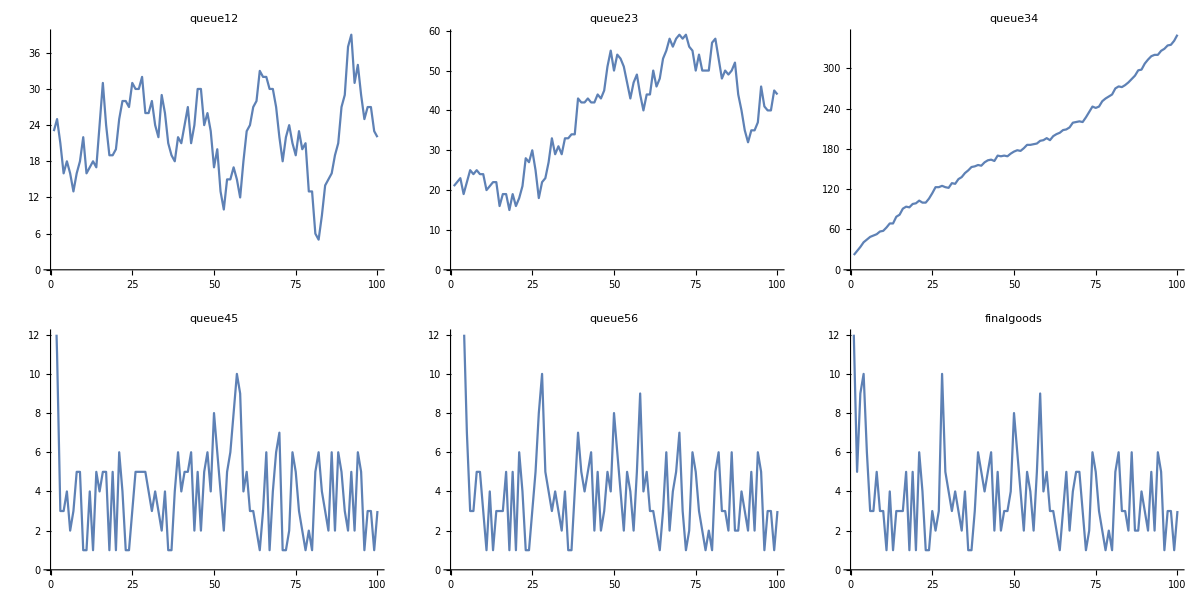

```mathematica
CL1QueueGraph
```

It is interesting to observe the tremendous almost linear growth of buffered material in queue 34. This queue is in front of the constraint. 
We have to remind ourselves that the constrained station is now reacting with a Uniform probability distribution compared to all other stations with a Gaussian distribution.

```mathematica
CL1QueueStat
```

### 4.4 Comparison of a) available and utilized capacities and b) last run WIP plus Final goods

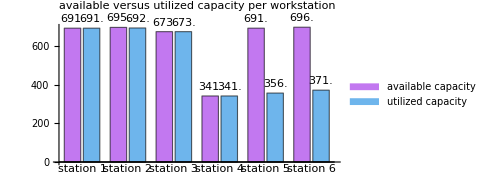
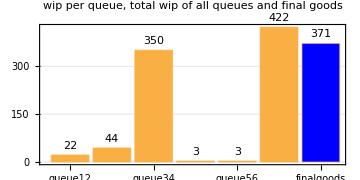
*        **        *-Graphics--Graphics-

```mathematica
Row[{plot1,plot2},"*        *"]
```

Let us try a simple explanation. Stations 1,2,3 know nothing about the constrained station 4, hence they produce as much as possible. The same is valid for station 4 but on a lower level. 
Stations 5 and 6 only get the lower output from station 4. Both stations are on a utilized capacity level of approx. 50%.
In this scenario we have much more work-in-process than as we have sold and shipped final goods. If we take no action, queue 34 will “linearly” grow forever.

### 4.5 Comparison of Throughput Accounting figures

```mathematica
financeCL1
```

## 5. TOC-DBR

TOC-DBR is an abbreviation that stands for TOC-Theory of Constraints with the application solution DBR Drum-Buffer-Rope.
Drum is the output of our constraint or to be more precisely: in operations, the schedule of the constraint.
Buffer is the protection against uncertainty for the constraint. In our case the material available in queue 34. In practice, it should be realized with active buffer management which is not integrated into this simulation.
Rope is a feedback loop or you can call it an information line. 

In this section, we will make use of the Rope to study its impact on the flow. It is very simple because we inform station 1 about the utilized capacity of station 4 of the former round. 
In the next round, station 1 will only release the amount of material that was moved from station 4 to station 5 in the previous round.

-Graphics-

### 5.1 Calculation part

```mathematica
dg=CL1;
Do[
dg[[i, 1]] = dg[[i, 1]];
                 dg[[i, 2]] = dg[[i, 2]] ;
                  If[i == 1,dg[[i, 3]] =dg[[i, 2]],dg[[i, 3]] =dg[[i-1,11]]];
                  If[i == 1,dg[[i, 4]] = startWipLevel,dg[[i, 4]] = dg[[i - 1, 4]] - dg[[i - 1, 6]] + dg[[i, 3]]];
dg[[i, 5]] = dg[[i, 5]];
                 dg[[i, 6]] =Min[dg[[i, 5]], dg[[i, 4]]];
                 If[i == 1, dg[[i, 7]] = dg[[i, 6]] + startWipLevel,dg[[i, 7]] = dg[[i - 1, 7]] - dg[[i - 1, 9]] + dg[[i, 6]]];
dg[[i, 8]] = dg[[i, 8]];
                dg[[i, 9]] = Min[dg[[i, 8]], dg[[i, 7]]];
                 If[i == 1,dg[[i, 10]] = dg[[i, 9]]+ startWipLevel*2, dg[[i, 10]] = dg[[i - 1, 10]] - dg[[i - 1, 12]] + dg[[i, 9]]];
dg[[i, 11]] = dg[[i, 11]];
                 dg[[i, 12]] = Min[dg[[i, 11]], dg[[i, 10]]];
                 If[i == 1, dg[[i, 13]] = dg[[i, 12]] + startWipLevel, dg[[i, 13]] = dg[[i - 1, 13]] - dg[[i - 1, 15]] + dg[[i, 12]]];
dg[[i, 14]] = dg[[i, 14]];
                 dg[[i, 15]] = Min[dg[[i, 14]], dg[[i, 13]]];
                 If[i == 1, dg[[i, 16]] = dg[[i, 15]] + startWipLevel , dg[[i, 16]] = dg[[i - 1, 16]] - dg[[i - 1, 18]] + dg[[i, 15]]];
dg[[i, 17]] = dg[[i, 17]];
                 dg[[i, 18]] = Min[dg[[i, 17]], dg[[i, 16]]];
                 dg[[i, 19]] = dg[[i,18]],
 {i,1,timeUnits,1}]
```

```mathematica
totalwipDBR=Total[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]]}];
finishedgoodsDBR=Total[dg[[All,19]]];
DBR=dg;
```

```mathematica
availCap=Table[N[Total[dg[[All,3*i-1]]]],{i,1,6}];
utilCap=Table[N[Total[dg[[All,3*i]]]],{i,1,6}];
```

```mathematica
plot1=BarChart[<|"station 1"-><|"avail."->availCap[[1]],"util."->utilCap[[1]]|>,
"station  2"-><|"avail."->availCap[[2]],"util."->utilCap[[2]]|>,
"station  3"-><|"avail."->availCap[[3]],"util."->utilCap[[3]]|>,
"station  4"-><|"avail."->availCap[[4]],"util."->utilCap[[4]]|>,
"station  5"-><|"avail."->availCap[[5]],"util."->utilCap[[5]]|>,
"station  6"-><|"avail."->availCap[[6]],"util."->utilCap[[6]]|> |>,
ChartStyle->"Pastel",
PlotLabel->"available versus utilized capacity per workstation",
ChartLegends->Placed[{"available capacity","utilized capacity"},Below],ChartLabels->{{"station 1","station 2","station 3","station 4","station 5","station 6"},None},
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];

plot2=BarChart[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]],Total[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]]}],Style[Total[dg[[All,19]]],Blue]},ChartLabels->{"queue12","queue23","queue34","queue45","queue56","totalwip","finalgoods"},
PlotTheme->"Business",
PlotLabel->"wip per queue, total wip of all queues and final goods",
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];

DBRRollingStat=Dataset[{
<|
"Min"-><|"station 1"->N[Min[dg[[All, 2]]]],"station 2"->N[Min[dg[[All, 5]]]],"station 3"->N[Min[dg[[All, 8]]]],"station 4"->N[Min[dg[[All,11]]]],"station 5"->N[Min[dg[[All,14]]]],"station 6"->N[Min[dg[[All,17]]]]|>,
"Mean"-><|"station 1"->N[Mean[dg[[All, 2]]]],"station 2"->N[Mean[dg[[All, 5]]]],"station 3"->N[Mean[dg[[All, 8]]]],"station 4"->N[Mean[dg[[All,11]]]],"station 5"->N[Mean[dg[[All,14]]]],"station 6"->N[Mean[dg[[All,17]]]]|>,
"Median"-><|"station 1"->N[Median[dg[[All, 2]]]],"station 2"->N[Median[dg[[All, 5]]]],"station 3"->N[Median[dg[[All, 8]]]],"station 4"->N[Median[dg[[All,11]]]],"station 5"->N[Median[dg[[All,14]]]],"station 6"->N[Median[dg[[All,17]]]]|>,
"StandardDeviation"-><|"station 1"->N[StandardDeviation[dg[[All, 2]]]],"station 2"->N[StandardDeviation[dg[[All, 5]]]],"station 3"->N[StandardDeviation[dg[[All, 8]]]],"station 4"->N[StandardDeviation[dg[[All,11]]]],"station 5"->N[StandardDeviation[dg[[All,14]]]],"station 6"->N[StandardDeviation[dg[[All,17]]]]|>,
"Variance"-><|"station 1"->N[Variance[dg[[All, 2]]]],"station 2"->N[Variance[dg[[All, 5]]]],"station 3"->N[Variance[dg[[All, 8]]]],"station 4"->N[Variance[dg[[All,11]]]],"station 5"->N[Variance[dg[[All,14]]]],"station 6"->N[Variance[dg[[All,17]]]]|>,
"Max"-><|"station 1"->N[Max[dg[[All, 2]]]],"station 2"->N[Max[dg[[All, 5]]]],"station 3"->N[Max[dg[[All, 8]]]],"station 4"->N[Max[dg[[All,11]]]],"station 5"->N[Max[dg[[All,14]]]],"station 6"->N[Max[dg[[All,17]]]]|>
|>},HeaderBackground->Pink];

DBRQueueStat=Dataset[{
<|
"Min"-><|"queue 12"->N[Min[dg[[All, 4]]]],"queue 23"->N[Min[dg[[All, 7]]]],"queue 34"->N[Min[dg[[All, 10]]]],"queue 45"->N[Min[dg[[All,13]]]],"queue 56"->N[Min[dg[[All,16]]]],"final goods"->N[Min[dg[[All,18]]]]|>,
"Mean"-><|"queue 12"->N[Mean[dg[[All, 4]]]],"queue 23"->N[Mean[dg[[All, 7]]]],"queue 34"->N[Mean[dg[[All, 10]]]],"queue 45"->N[Mean[dg[[All,13]]]],"queue 56"->N[Mean[dg[[All,16]]]],"final goods"->N[Mean[dg[[All,18]]]]|>,
"Median"-><|"queue 12"->N[Median[dg[[All, 4]]]],"queue 23"->N[Median[dg[[All, 7]]]],"queue 34"->N[Median[dg[[All, 10]]]],"queue 45"->N[Median[dg[[All,13]]]],"queue 56"->N[Median[dg[[All,16]]]],"final goods"->N[Median[dg[[All,18]]]]|>,
"StandardDeviation"-><|"queue 12"->N[StandardDeviation[dg[[All, 4]]]],"queue 23"->N[StandardDeviation[dg[[All, 7]]]],"queue 34"->N[StandardDeviation[dg[[All, 10]]]],"queue 45"->N[StandardDeviation[dg[[All,13]]]],"queue 56"->N[StandardDeviation[dg[[All,16]]]],"final goods"->N[StandardDeviation[dg[[All,18]]]]|>,
"Variance"-><|"queue 12"->N[Variance[dg[[All, 4]]]],"queue 23"->N[Variance[dg[[All, 7]]]],"queue 34"->N[Variance[dg[[All, 10]]]],"queue 45"->N[Variance[dg[[All,13]]]],"queue 56"->N[Variance[dg[[All,16]]]],"final goods"->N[Variance[dg[[All,18]]]]|>,
"Max"-><|"queue 12"->N[Max[dg[[All, 4]]]],"queue 23"->N[Max[dg[[All, 7]]]],"queue 34"->N[Max[dg[[All, 10]]]],"queue 45"->N[Max[dg[[All,13]]]],"queue 56"->N[Max[dg[[All,16]]]],"final goods"->N[Max[dg[[All,18]]]]|>
|>},HeaderBackground->LightBlue];

DBRQueueGraph=TableForm[{{ListLinePlot[dg[[All,4]],PlotLabel->"queue12"],ListLinePlot[dg[[All,7]],PlotLabel->"queue23"],ListLinePlot[dg[[All,10]],PlotLabel->"queue34"]},{ListLinePlot[dg[[All,13]],PlotLabel->"queue45"],ListLinePlot[dg[[All,16]],PlotLabel->"queue56"],ListLinePlot[dg[[All,18]],PlotLabel->"finalgoods"]}},1];

TDBR=(sp-tvc)*finishedgoodsDBR; 
IDBR=(totalwipDBR*tvc)+invest;
npDBR=TDBR-oe;
roiDBR=PercentForm[npDBR/IDBR / 100];
csDBR=PercentForm[1.];
ltDBR=(totalwipDBR / finishedgoodsDBR / timeUnits);
pDBR=TDBR/oe;
itDBR=finishedgoodsDBR / totalwipDBR ;

financeDBR=Dataset[{
<| "Throughput"-><|"Balanced Line"->N[TBL1],"Constrained Line"->N[TCL1],"TOC-DBR"->N[TDBR]|>,
"Inventory"-><|"Balanced Line"->N[IBL1],"Constrained Line"->N[ICL1],"TOC-DBR"->N[IDBR]|>,
"Operating Expenses"-><|"Balanced Line"->N[oe],"Constrained Line"->N[oe],"TOC-DBR"->N[oe]|>,
"Net Profit"-><|"Balanced Line"->N[npBL1],"Constrained Line"->N[npCL1],"TOC-DBR"->N[npDBR]|>,
"ROI"-><|"Balanced Line"->N[roiBL1],"Constrained Line"->N[roiCL1],"TOC-DBR"->N[roiDBR]|>,
"Customer Service"-><|"Balanced Line"->N[csBL1],"Constrained Line"->N[csCL1],"TOC-DBR"->N[csDBR]|>,
"Productivity"-><|"Balanced Line"->N[pBL1],"Constrained Line"->N[pCL1],"TOC-DBR"->N[pDBR]|>,
"Inventory Turnover"-><|"Balanced Line"->N[itBL1],"Constrained Line"->N[itCL1],"TOC-DBR"->N[itDBR]|>
|>},HeaderBackground->LightGreen];
```

### 5.2 Rolling dice statistics

In this scenario, we re-use all rolled dice points, but we modify the program code to make use of the information via the rope.

```mathematica
DBRRollingStat
```

### 5.3 Queue statistics

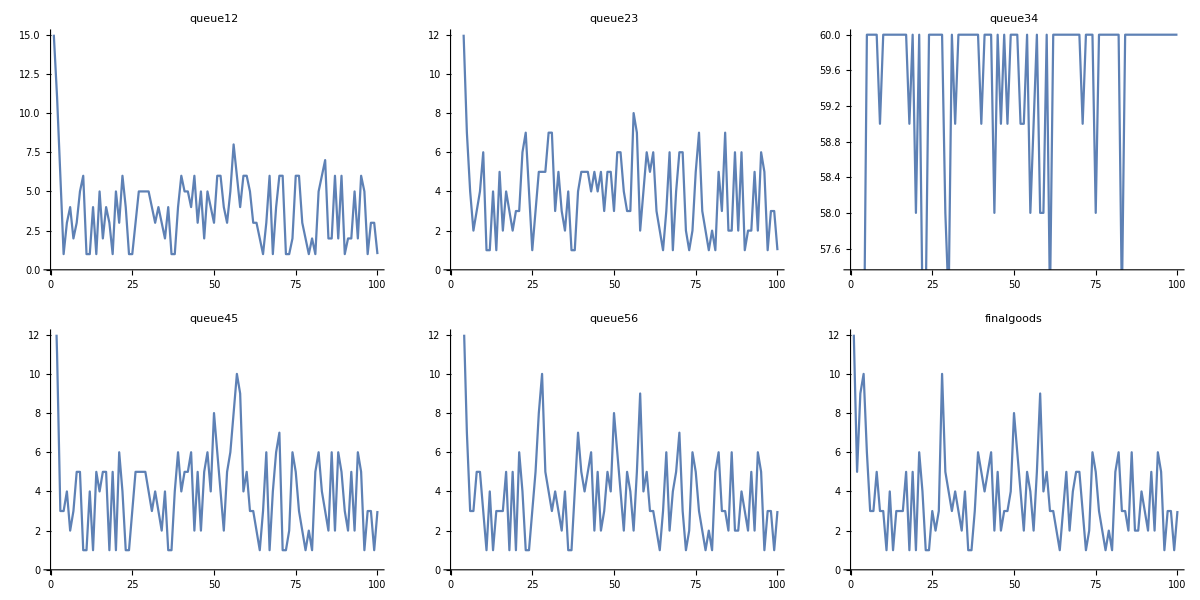

```mathematica
DBRQueueGraph
```

```mathematica
DBRQueueStat
```

### 5.4 Comparison of a) available and utilized capacities and b) last run WIP plus Final goods

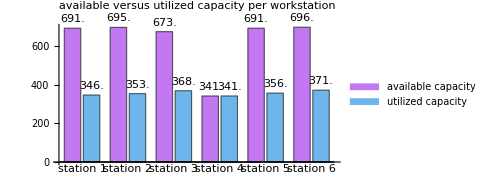
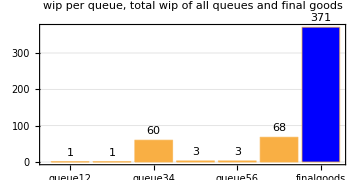
*        **        *-Graphics--Graphics-

```mathematica
Row[{plot1,plot2},"*        *"]
```

Apart from station 4, the utilized capacities of all other stations are significantly reduced.
More important is that the work-in-process could be reduced from 422 pieces to 68 units.

### 5.5 Comparison of Throughput Accounting figures

```mathematica
financeDBR
```

Okay, in this step we did not increase the Throughput, but we could significantly reduce WIP and therefore we get a much lower Inventory.

The Rope launch does typically belong to step 3 of the Five Focusing Steps: 3. Subordinate Everything Else to the Constraint

For didactical reasons, I decided to launch the Rope first and we will make use of it in the following scenarios.

## 6. TLS

TLS is an abbreviation for Theory of Constraints, Lean, and Six Sigma. These three improvement methodologies are known in operations management. Each methodology has its own advantages. 
By using the term TLS it is meant to take the best from each method and combine them.

In this section, we apply TLS at our constraint to full-fill step number 2 of the Five Focusing Steps: 2. Exploit the Constraint

-Graphics-

Let us assume that we could stabilize the process of station 4 with the help of Lean and Six Sigma. The result is a lower variance. We can (only) roll now a 4, 5, or 6. This action should allow us to increase the Throughput.

### 6.1 Calculation part

```mathematica
dg=BL1;
Do[
dg[[i, 1]] = dg[[i, 1]];
                 dg[[i, 2]] = dg[[i, 2]] ;
                  If[i == 1,dg[[i, 3]] =dg[[i, 2]],dg[[i, 3]] =dg[[i-1,11]]];
                  If[i == 1,dg[[i, 4]] = startWipLevel,dg[[i, 4]] = dg[[i - 1, 4]] - dg[[i - 1, 6]] + dg[[i, 3]]];
dg[[i, 5]] = dg[[i, 5]];
                 dg[[i, 6]] =Min[dg[[i, 5]], dg[[i, 4]]];
                 If[i == 1, dg[[i, 7]] = dg[[i, 6]] + startWipLevel,dg[[i, 7]] = dg[[i - 1, 7]] - dg[[i - 1, 9]] + dg[[i, 6]]];
dg[[i, 8]] = dg[[i, 8]];
                dg[[i, 9]] = Min[dg[[i, 8]], dg[[i, 7]]];
                 If[i == 1,dg[[i, 10]] = dg[[i, 9]]+ startWipLevel*2, dg[[i, 10]] = dg[[i - 1, 10]] - dg[[i - 1, 12]] + dg[[i, 9]]];
dg[[i, 11]] = Total[RandomInteger[{4,6},1]];
                 dg[[i, 12]] = Min[dg[[i, 11]], dg[[i, 10]]];
                 If[i == 1, dg[[i, 13]] = dg[[i, 12]] + startWipLevel, dg[[i, 13]] = dg[[i - 1, 13]] - dg[[i - 1, 15]] + dg[[i, 12]]];
dg[[i, 14]] = dg[[i, 14]];
                 dg[[i, 15]] = Min[dg[[i, 14]], dg[[i, 13]]];
                 If[i == 1, dg[[i, 16]] = dg[[i, 15]] + startWipLevel , dg[[i, 16]] = dg[[i - 1, 16]] - dg[[i - 1, 18]] + dg[[i, 15]]];
dg[[i, 17]] = dg[[i, 17]];
                 dg[[i, 18]] = Min[dg[[i, 17]], dg[[i, 16]]];
                 dg[[i, 19]] = dg[[i,18]],
 {i,1,timeUnits,1}]
```

```mathematica
totalWIPTLS=Total[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]]}];
```

```mathematica
finishedgoodsTLS=Total[dg[[All,19]]];
TLS=dg;
```

```mathematica
availCap=Table[N[Total[dg[[All,3*i-1]]]],{i,1,6}];
utilCap=Table[N[Total[dg[[All,3*i]]]],{i,1,6}];
```

```mathematica
plot1=BarChart[<|"station 1"-><|"avail."->availCap[[1]],"util."->utilCap[[1]]|>,
"station  2"-><|"avail."->availCap[[2]],"util."->utilCap[[2]]|>,
"station  3"-><|"avail."->availCap[[3]],"util."->utilCap[[3]]|>,
"station  4"-><|"avail."->availCap[[4]],"util."->utilCap[[4]]|>,
"station  5"-><|"avail."->availCap[[5]],"util."->utilCap[[5]]|>,
"station  6"-><|"avail."->availCap[[6]],"util."->utilCap[[6]]|> |>,
ChartStyle->"Pastel",
PlotLabel->"available versus utilized capacity per workstation",
ChartLegends->Placed[{"available capacity","utilized capacity"},Below],ChartLabels->{{"station 1","station 2","station 3","station 4","station 5","station 6"},None},
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];

plot2=BarChart[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]],Total[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]]}],Style[Total[dg[[All,19]]],Blue]},ChartLabels->{"queue12","queue23","queue34","queue45","queue56","totalWIP","finalgoods"},
PlotTheme->"Business",
PlotLabel->"WIP per queue, total WIP of all queues and final goods",
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];

TLSRollingStat=Dataset[{
<|
"Min"-><|"station 1"->N[Min[dg[[All, 2]]]],"station 2"->N[Min[dg[[All, 5]]]],"station 3"->N[Min[dg[[All, 8]]]],"station 4"->N[Min[dg[[All,11]]]],"station 5"->N[Min[dg[[All,14]]]],"station 6"->N[Min[dg[[All,17]]]]|>,
"Mean"-><|"station 1"->N[Mean[dg[[All, 2]]]],"station 2"->N[Mean[dg[[All, 5]]]],"station 3"->N[Mean[dg[[All, 8]]]],"station 4"->N[Mean[dg[[All,11]]]],"station 5"->N[Mean[dg[[All,14]]]],"station 6"->N[Mean[dg[[All,17]]]]|>,
"Median"-><|"station 1"->N[Median[dg[[All, 2]]]],"station 2"->N[Median[dg[[All, 5]]]],"station 3"->N[Median[dg[[All, 8]]]],"station 4"->N[Median[dg[[All,11]]]],"station 5"->N[Median[dg[[All,14]]]],"station 6"->N[Median[dg[[All,17]]]]|>,
"StandardDeviation"-><|"station 1"->N[StandardDeviation[dg[[All, 2]]]],"station 2"->N[StandardDeviation[dg[[All, 5]]]],"station 3"->N[StandardDeviation[dg[[All, 8]]]],"station 4"->N[StandardDeviation[dg[[All,11]]]],"station 5"->N[StandardDeviation[dg[[All,14]]]],"station 6"->N[StandardDeviation[dg[[All,17]]]]|>,
"Variance"-><|"station 1"->N[Variance[dg[[All, 2]]]],"station 2"->N[Variance[dg[[All, 5]]]],"station 3"->N[Variance[dg[[All, 8]]]],"station 4"->N[Variance[dg[[All,11]]]],"station 5"->N[Variance[dg[[All,14]]]],"station 6"->N[Variance[dg[[All,17]]]]|>,
"Max"-><|"station 1"->N[Max[dg[[All, 2]]]],"station 2"->N[Max[dg[[All, 5]]]],"station 3"->N[Max[dg[[All, 8]]]],"station 4"->N[Max[dg[[All,11]]]],"station 5"->N[Max[dg[[All,14]]]],"station 6"->N[Max[dg[[All,17]]]]|>
|>},HeaderBackground->Pink];

TLSQueueStat=Dataset[{
<|
"Min"-><|"queue 12"->N[Min[dg[[All, 4]]]],"queue 23"->N[Min[dg[[All, 7]]]],"queue 34"->N[Min[dg[[All, 10]]]],"queue 45"->N[Min[dg[[All,13]]]],"queue 56"->N[Min[dg[[All,16]]]],"final goods"->N[Min[dg[[All,18]]]]|>,
"Mean"-><|"queue 12"->N[Mean[dg[[All, 4]]]],"queue 23"->N[Mean[dg[[All, 7]]]],"queue 34"->N[Mean[dg[[All, 10]]]],"queue 45"->N[Mean[dg[[All,13]]]],"queue 56"->N[Mean[dg[[All,16]]]],"final goods"->N[Mean[dg[[All,18]]]]|>,
"Median"-><|"queue 12"->N[Median[dg[[All, 4]]]],"queue 23"->N[Median[dg[[All, 7]]]],"queue 34"->N[Median[dg[[All, 10]]]],"queue 45"->N[Median[dg[[All,13]]]],"queue 56"->N[Median[dg[[All,16]]]],"final goods"->N[Median[dg[[All,18]]]]|>,
"StandardDeviation"-><|"queue 12"->N[StandardDeviation[dg[[All, 4]]]],"queue 23"->N[StandardDeviation[dg[[All, 7]]]],"queue 34"->N[StandardDeviation[dg[[All, 10]]]],"queue 45"->N[StandardDeviation[dg[[All,13]]]],"queue 56"->N[StandardDeviation[dg[[All,16]]]],"final goods"->N[StandardDeviation[dg[[All,18]]]]|>,
"Variance"-><|"queue 12"->N[Variance[dg[[All, 4]]]],"queue 23"->N[Variance[dg[[All, 7]]]],"queue 34"->N[Variance[dg[[All, 10]]]],"queue 45"->N[Variance[dg[[All,13]]]],"queue 56"->N[Variance[dg[[All,16]]]],"final goods"->N[Variance[dg[[All,18]]]]|>,
"Max"-><|"queue 12"->N[Max[dg[[All, 4]]]],"queue 23"->N[Max[dg[[All, 7]]]],"queue 34"->N[Max[dg[[All, 10]]]],"queue 45"->N[Max[dg[[All,13]]]],"queue 56"->N[Max[dg[[All,16]]]],"final goods"->N[Max[dg[[All,18]]]]|>
|>},HeaderBackground->LightBlue];

TLSQueueGraph=TableForm[{{ListLinePlot[dg[[All,4]],PlotLabel->"queue12"],ListLinePlot[dg[[All,7]],PlotLabel->"queue23"],ListLinePlot[dg[[All,10]],PlotLabel->"queue34"]},{ListLinePlot[dg[[All,13]],PlotLabel->"queue45"],ListLinePlot[dg[[All,16]],PlotLabel->"queue56"],ListLinePlot[dg[[All,18]],PlotLabel->"finalgoods"]}},1];

TTLS=(sp-tvc)*finishedgoodsTLS; 
ITLS=(totalWIPTLS*tvc)+invest;
npTLS=TTLS-oe;
roiTLS=PercentForm[npTLS/ITLS / 100];
csTLS=PercentForm[1.];
ltTLS=(totalWIPTLS / finishedgoodsTLS / timeUnits);
pTLS=TTLS/oe;
itTLS=finishedgoodsTLS / totalWIPTLS ;

financeTLS=Dataset[{
<| "Throughput"-><|"Balanced Line"->N[TBL1],"Constrained Line"->N[TCL1],"TOC-DBR"->N[TDBR],"TLS"->N[TTLS]|>,
"Inventory"-><|"Balanced Line"->N[IBL1],"Constrained Line"->N[ICL1],"TOC-DBR"->N[IDBR],"TLS"->N[ITLS]|>,
"Operating Expenses"-><|"Balanced Line"->N[oe],"Constrained Line"->N[oe],"TOC-DBR"->N[oe],"TLS"->N[oe]|>,
"Net Profit"-><|"Balanced Line"->N[npBL1],"Constrained Line"->N[npCL1],"TOC-DBR"->N[npDBR],"TLS"->N[npTLS]|>,
"ROI"-><|"Balanced Line"->N[roiBL1],"Constrained Line"->N[roiCL1],"TOC-DBR"->N[roiDBR],"TLS"->N[roiTLS]|>,
"Customer Service"-><|"Balanced Line"->N[csBL1],"Constrained Line"->N[csCL1],"TOC-DBR"->N[csDBR],"TLS"->N[csTLS]|>,
"Productivity"-><|"Balanced Line"->N[pBL1],"Constrained Line"->N[pCL1],"TOC-DBR"->N[pDBR],"TLS"->N[pTLS]|>,
"Inventory Turnover"-><|"Balanced Line"->N[itBL1],"Constrained Line"->N[itCL1],"TOC-DBR"->N[itDBR],"TLS"->N[itTLS]|>
|>},HeaderBackground->LightGreen];
```

### 6.2 Rolling dice statistics

```mathematica
TLSRollingStat
```

The Rolling Dice Statistics shows a higher mean, median, and much lower variance for station 4.

### 6.3 Queue statistics

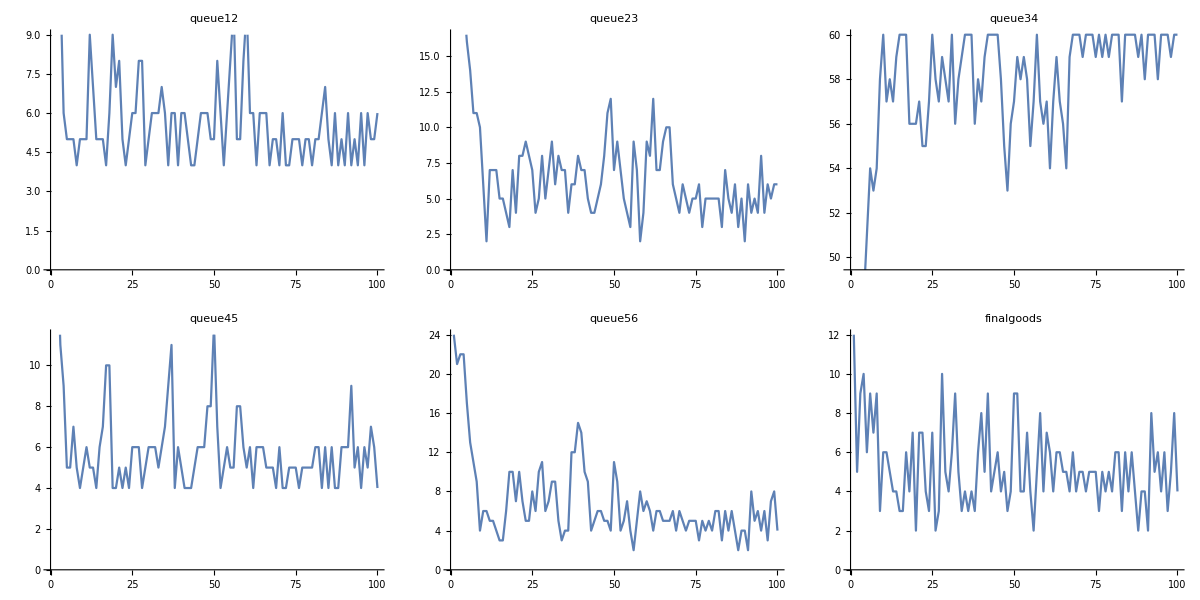

```mathematica
TLSQueueGraph
```

```mathematica
TLSQueueStat
```

### 6.4 Comparison of a) available and utilized capacities and b) last run WIP plus Final goods

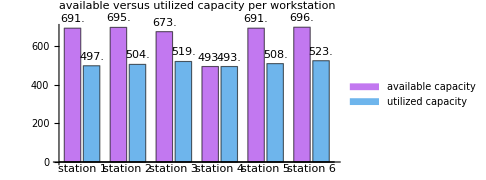
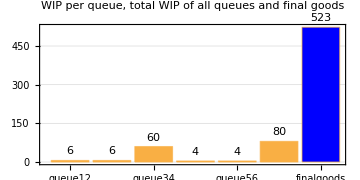
*        **        *-Graphics--Graphics-

```mathematica
Row[{plot1,plot2},"*        *"]
```

6.5 Comparison of Throughput Accounting figures

```mathematica
financeTLS
```

## 7. Full TOC

The term Full TOC is invented by the author to describe the next step of the Five Focusing Steps: 4. Elevate the Constraint. After all these improvement steps the moment has come to invest some money to enlarge the capacity of station 4, but not earlier.
With a further focus on Lean and Six Sigma improvement opportunities and the investment in one new dice, we can further improve the Throughput of our system.
Our invest goes into four-sided dice that allows us to roll either a 5, 6, 7, or 8.

-Graphics-

### 7.1 Calculation part

```mathematica
Clear[dg];
```

```mathematica
dg=BL1;
Do[
dg[[i, 1]] = dg[[i, 1]];
                 dg[[i, 2]] = dg[[i, 2]] ;
                  If[i == 1,dg[[i, 3]] =dg[[i, 2]],dg[[i, 3]] =dg[[i-1,11]]];
                  If[i == 1,dg[[i, 4]] = startWipLevel,dg[[i, 4]] = dg[[i - 1, 4]] - dg[[i - 1, 6]] + dg[[i, 3]]];
dg[[i, 5]] = dg[[i, 5]];
                 dg[[i, 6]] =Min[dg[[i, 5]], dg[[i, 4]]];
                 If[i == 1, dg[[i, 7]] = dg[[i, 6]] + startWipLevel,dg[[i, 7]] = dg[[i - 1, 7]] - dg[[i - 1, 9]] + dg[[i, 6]]];
dg[[i, 8]] = dg[[i, 8]];
                dg[[i, 9]] = Min[dg[[i, 8]], dg[[i, 7]]];
                 If[i == 1,dg[[i, 10]] = dg[[i, 9]]+ startWipLevel*2, dg[[i, 10]] = dg[[i - 1, 10]] - dg[[i - 1, 12]] + dg[[i, 9]]];
dg[[i, 11]] = Total[RandomInteger[{5,8},1]];
                 dg[[i, 12]] = Min[dg[[i, 11]], dg[[i, 10]]];
                 If[i == 1, dg[[i, 13]] = dg[[i, 12]] + startWipLevel, dg[[i, 13]] = dg[[i - 1, 13]] - dg[[i - 1, 15]] + dg[[i, 12]]];
dg[[i, 14]] = dg[[i, 14]];
                 dg[[i, 15]] = Min[dg[[i, 14]], dg[[i, 13]]];
                 If[i == 1, dg[[i, 16]] = dg[[i, 15]] + startWipLevel , dg[[i, 16]] = dg[[i - 1, 16]] - dg[[i - 1, 18]] + dg[[i, 15]]];
dg[[i, 17]] = dg[[i, 17]];
                 dg[[i, 18]] = Min[dg[[i, 17]], dg[[i, 16]]];
                 dg[[i, 19]] = dg[[i,18]],
 {i,1,timeUnits,1}]
```

```mathematica
totalwipfulltoc=Total[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]]}];
finishedgoodsfulltoc=Total[dg[[All,19]]];
fulltoc=dg;
```

```mathematica
availCap=Table[N[Total[dg[[All,3*i-1]]]],{i,1,6}];
utilCap=Table[N[Total[dg[[All,3*i]]]],{i,1,6}];
```

```mathematica
plot1=BarChart[<|"station 1"-><|"avail."->availCap[[1]],"util."->utilCap[[1]]|>,
"station  2"-><|"avail."->availCap[[2]],"util."->utilCap[[2]]|>,
"station  3"-><|"avail."->availCap[[3]],"util."->utilCap[[3]]|>,
"station  4"-><|"avail."->availCap[[4]],"util."->utilCap[[4]]|>,
"station  5"-><|"avail."->availCap[[5]],"util."->utilCap[[5]]|>,
"station  6"-><|"avail."->availCap[[6]],"util."->utilCap[[6]]|> |>,
ChartStyle->"Pastel",
PlotLabel->"available versus utilized capacity per workstation",
ChartLegends->Placed[{"available capacity","utilized capacity"},Below],ChartLabels->{{"station 1","station 2","station 3","station 4","station 5","station 6"},None},
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];

plot2=BarChart[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]],Total[{dg[[timeUnits,4]],dg[[timeUnits,7]],dg[[timeUnits,10]],dg[[timeUnits,13]],dg[[timeUnits,16]]}],Style[Total[dg[[All,19]]],Blue]},ChartLabels->{"queue12","queue23","queue34","queue45","queue56","totalWIP","finalgoods"},
PlotTheme->"Business",
PlotLabel->"WIP per queue, total WIP of all queues and Final Goods",
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];

FullTOCRollingStat=Dataset[{
<|
"Min"-><|"station 1"->N[Min[dg[[All, 2]]]],"station 2"->N[Min[dg[[All, 5]]]],"station 3"->N[Min[dg[[All, 8]]]],"station 4"->N[Min[dg[[All,11]]]],"station 5"->N[Min[dg[[All,14]]]],"station 6"->N[Min[dg[[All,17]]]]|>,
"Mean"-><|"station 1"->N[Mean[dg[[All, 2]]]],"station 2"->N[Mean[dg[[All, 5]]]],"station 3"->N[Mean[dg[[All, 8]]]],"station 4"->N[Mean[dg[[All,11]]]],"station 5"->N[Mean[dg[[All,14]]]],"station 6"->N[Mean[dg[[All,17]]]]|>,
"Median"-><|"station 1"->N[Median[dg[[All, 2]]]],"station 2"->N[Median[dg[[All, 5]]]],"station 3"->N[Median[dg[[All, 8]]]],"station 4"->N[Median[dg[[All,11]]]],"station 5"->N[Median[dg[[All,14]]]],"station 6"->N[Median[dg[[All,17]]]]|>,
"StandardDeviation"-><|"station 1"->N[StandardDeviation[dg[[All, 2]]]],"station 2"->N[StandardDeviation[dg[[All, 5]]]],"station 3"->N[StandardDeviation[dg[[All, 8]]]],"station 4"->N[StandardDeviation[dg[[All,11]]]],"station 5"->N[StandardDeviation[dg[[All,14]]]],"station 6"->N[StandardDeviation[dg[[All,17]]]]|>,
"Variance"-><|"station 1"->N[Variance[dg[[All, 2]]]],"station 2"->N[Variance[dg[[All, 5]]]],"station 3"->N[Variance[dg[[All, 8]]]],"station 4"->N[Variance[dg[[All,11]]]],"station 5"->N[Variance[dg[[All,14]]]],"station 6"->N[Variance[dg[[All,17]]]]|>,
"Max"-><|"station 1"->N[Max[dg[[All, 2]]]],"station 2"->N[Max[dg[[All, 5]]]],"station 3"->N[Max[dg[[All, 8]]]],"station 4"->N[Max[dg[[All,11]]]],"station 5"->N[Max[dg[[All,14]]]],"station 6"->N[Max[dg[[All,17]]]]|>
|>},HeaderBackground->Pink];

FullTOCQueueStat=Dataset[{
<|
"Min"-><|"queue 12"->N[Min[dg[[All, 4]]]],"queue 23"->N[Min[dg[[All, 7]]]],"queue 34"->N[Min[dg[[All, 10]]]],"queue 45"->N[Min[dg[[All,13]]]],"queue 56"->N[Min[dg[[All,16]]]],"final goods"->N[Min[dg[[All,18]]]]|>,
"Mean"-><|"queue 12"->N[Mean[dg[[All, 4]]]],"queue 23"->N[Mean[dg[[All, 7]]]],"queue 34"->N[Mean[dg[[All, 10]]]],"queue 45"->N[Mean[dg[[All,13]]]],"queue 56"->N[Mean[dg[[All,16]]]],"final goods"->N[Mean[dg[[All,18]]]]|>,
"Median"-><|"queue 12"->N[Median[dg[[All, 4]]]],"queue 23"->N[Median[dg[[All, 7]]]],"queue 34"->N[Median[dg[[All, 10]]]],"queue 45"->N[Median[dg[[All,13]]]],"queue 56"->N[Median[dg[[All,16]]]],"final goods"->N[Median[dg[[All,18]]]]|>,
"StandardDeviation"-><|"queue 12"->N[StandardDeviation[dg[[All, 4]]]],"queue 23"->N[StandardDeviation[dg[[All, 7]]]],"queue 34"->N[StandardDeviation[dg[[All, 10]]]],"queue 45"->N[StandardDeviation[dg[[All,13]]]],"queue 56"->N[StandardDeviation[dg[[All,16]]]],"final goods"->N[StandardDeviation[dg[[All,18]]]]|>,
"Variance"-><|"queue 12"->N[Variance[dg[[All, 4]]]],"queue 23"->N[Variance[dg[[All, 7]]]],"queue 34"->N[Variance[dg[[All, 10]]]],"queue 45"->N[Variance[dg[[All,13]]]],"queue 56"->N[Variance[dg[[All,16]]]],"final goods"->N[Variance[dg[[All,18]]]]|>,
"Max"-><|"queue 12"->N[Max[dg[[All, 4]]]],"queue 23"->N[Max[dg[[All, 7]]]],"queue 34"->N[Max[dg[[All, 10]]]],"queue 45"->N[Max[dg[[All,13]]]],"queue 56"->N[Max[dg[[All,16]]]],"final goods"->N[Max[dg[[All,18]]]]|>
|>},HeaderBackground->LightBlue];

FullTOCQueueGraph=TableForm[{{ListLinePlot[dg[[All,4]],PlotLabel->"queue12"],ListLinePlot[dg[[All,7]],PlotLabel->"queue23"],ListLinePlot[dg[[All,10]],PlotLabel->"queue34"]},{ListLinePlot[dg[[All,13]],PlotLabel->"queue45"],ListLinePlot[dg[[All,16]],PlotLabel->"queue56"],ListLinePlot[dg[[All,18]],PlotLabel->"finalgoods"]}},1];

TFullTOC=(sp-tvc)*finishedgoodsfulltoc; 
IFullTOC=(totalwipfulltoc*tvc)+invest+10000;
npFullTOC=TFullTOC-oe;
roiFullTOC=PercentForm[npFullTOC/IFullTOC / 100];
csFullTOC=PercentForm[1.];
ltFullTOC=(totalwipfulltoc/ finishedgoodsfulltoc / timeUnits);
pFullTOC=TFullTOC/oe;
itFullTOC=finishedgoodsfulltoc /totalwipfulltoc;

financeFullTOC=Dataset[{
<| "Throughput"-><|"Balanced Line"->N[TBL1],"Constrained Line"->N[TCL1],"TOC-DBR"->N[TDBR],"TLS"->N[TTLS],"Full TOC"->N[TFullTOC]|>,
"Inventory"-><|"Balanced Line"->N[IBL1],"Constrained Line"->N[ICL1],"TOC-DBR"->N[IDBR],"TLS"->N[ITLS],"Full TOC"->N[IFullTOC]|>,
"Operating Expenses"-><|"Balanced Line"->N[oe],"Constrained Line"->N[oe],"TOC-DBR"->N[oe],"TLS"->N[oe],"Full TOC"->N[oe]|>,
"Net Profit"-><|"Balanced Line"->N[npBL1],"Constrained Line"->N[npCL1],"TOC-DBR"->N[npDBR],"TLS"->N[npTLS],"Full TOC"->N[npFullTOC]|>,
"ROI"-><|"Balanced Line"->N[roiBL1],"Constrained Line"->N[roiCL1],"TOC-DBR"->N[roiDBR],"TLS"->N[roiTLS],"Full TOC"->N[roiFullTOC]|>,
"Customer Service"-><|"Balanced Line"->N[csBL1],"Constrained Line"->N[csCL1],"TOC-DBR"->N[csDBR],"TLS"->N[csTLS],"Full TOC"->N[csFullTOC]|>,
"Productivity"-><|"Balanced Line"->N[pBL1],"Constrained Line"->N[pCL1],"TOC-DBR"->N[pDBR],"TLS"->N[pTLS],"Full TOC"->N[pFullTOC]|>,
"Inventory Turnover"-><|"Balanced Line"->N[itBL1],"Constrained Line"->N[itCL1],"TOC-DBR"->N[itDBR],"TLS"->N[itTLS],"Full TOC"->N[itFullTOC]|>
|>},HeaderBackground->LightGreen];
```

### 7.2 Rolling dice statistics

```mathematica
FullTOCRollingStat
```

The Rolling Dice Statistics shows that with the new dice the mean, and median values of station 4 are almost the same compared to all other stations. Of course, the variance is still low.

### 7.3 Queue statistics

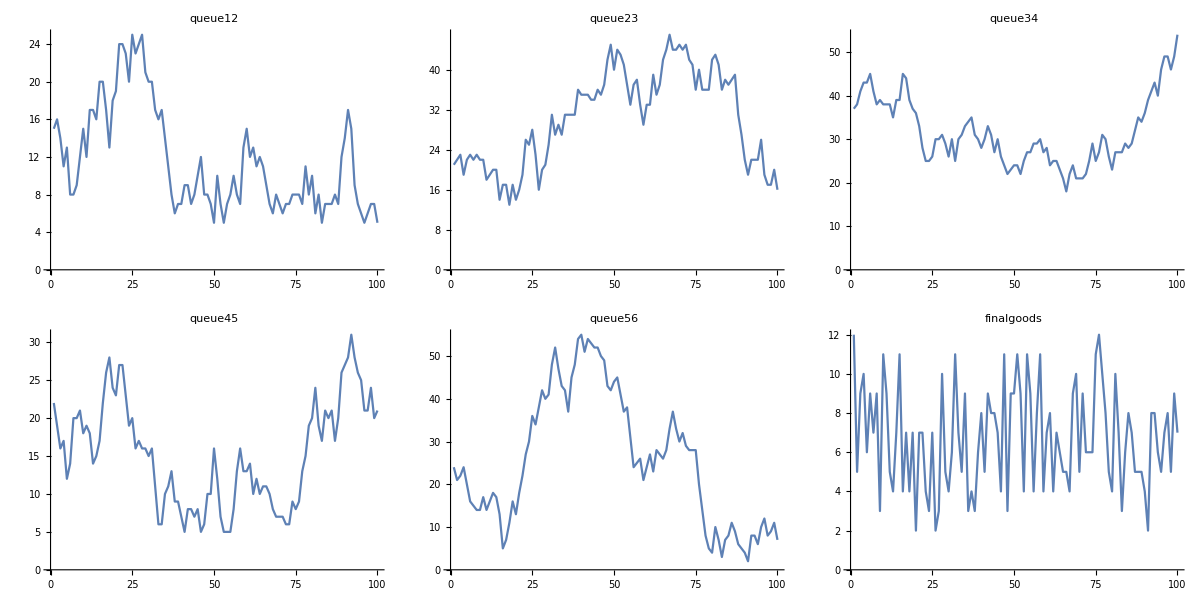

```mathematica
FullTOCQueueGraph
```

```mathematica
FullTOCQueueStat
```

### 7.4 Comparison of a) available and utilized capacities and b) last run WIP plus Final goods

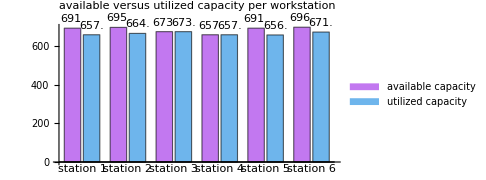
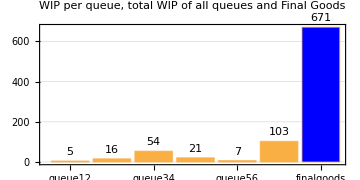
*        **        *-Graphics--Graphics-

```mathematica
Row[{plot1,plot2},"*        *"]
```

The available and utilized capacities are now on almost the same level. The level of Final Goods is high and the Ending WIP low.

7.5 Comparison of Throughput Accounting figures

```mathematica
financeFullTOC
```

In case you study the code, you will recognize that I have added a $10,000 investment for the new dice into the Inventory category. 
Nevertheless, our Throughput, Net Profit, Productivity, and Inventory Turnover is outstanding. Even compared to the Balanced Line that remains unconstrained. Great isn’t it?

## 8. Comparison of Final Results

### 8.1 Calculation part

```mathematica
plot1=BarChart[{totalwipBL1,totalwipCL1,totalwipDBR,totalWIPTLS,totalwipfulltoc},
ChartLabels->{"Bal. Line","Constr. Line","TOC DBR","TLS","Full TOC"},
PlotTheme->"Business",
PlotLabel->"amount of Ending WIP",
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];
```

```mathematica
plot2=BarChart[Style[{finishedgoodsBL1,finishedgoodsCL1,finishedgoodsDBR,finishedgoodsTLS, finishedgoodsfulltoc},Blue],ChartLabels->{"Bal. Line","Constr. Line","TOC DBR","TLS","Full TOC"},
PlotTheme->"Business",
PlotLabel->"amount of Final Goods",
LabelingFunction->Above,
AspectRatio->0.5,
ImageSize->Medium
 ];
```

### 8.2 Comparison of Ending WIP and Final goods

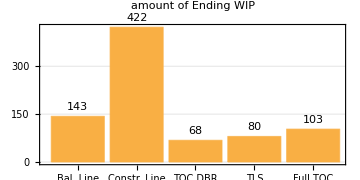
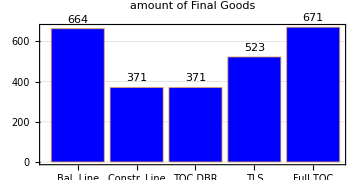
*        **        *-Graphics--Graphics-

```mathematica
Row[{plot1,plot2},"*        *"]
```

### 8.3 Comparison of Throughput Accounting figures

```mathematica
financeFullTOC
```

Still amazing results, right?

## 9. POOGI

POOGI is the abbreviation for Process Of OnGoing Improvement. What does it mean?

So far we did not finish our Five Focusing Steps approach. Step 5. Prevent Inertia from Becoming the Constraint has not been realized yet. 
It often happens that managers are happy we the results achieved by Full TOC and they leave it as it is. In such a moment human Inertia is triggered and the attention moves to other areas of interest. It would be much better and re-focus on the work that has been done and to further improve the system or a new constraint may pop up somewhere else. 
Step 5 is a warning sign. It means to go back to step 1 of the Five Focusing Steps and seek the next constraint. If you do this repeatedly you are automatically in POOGI.